## This notebook requires the NCAlgebra package available at http://math.ucsd.edu/~ncalg/. The NCSE package for NCAlgebra is needed for the example in the notebook but is not required to use the main functions in the notebook. Relevant paper: https://arxiv.org/abs/2008.13250

NC, NCAlgebra, and NCGBX are all contained in the main NCAlgebra package. These packages are necessary for computing the NC polynomials which define the Arveson boundary of a given free quadrilateral. 
The NCSE package is an additional user made package for NCAlgebra which is used for working with extreme points of free spectrahedra. This package is not necessary for computation of NC polynomials; however some of its functions are used in the example.
Warning: NCSE uses the convention L_A (X) = Identity - Lambda_A (X) rather than the L_A (X) = Identity + Lambda_A (X) convention used in the article associated to this notebook. To solve this issue, a defining tuple “A” is input into NCSE functions as “-A” so that in NCSE we have L_-A (X) = Identity+Lambda_A (X).

```mathematica
<<NC`
<<NCAlgebra`
<<NCGBX`
<<NCSE`
```

You are using the version of NCAlgebra which is found in:

C:\Users\Eric\NC\

You can now use "<< NCAlgebra`" to load NCAlgebra.

## Main functions.

This section contains all functions associated with this notebook.

```mathematica
NCSquare = {DiagonalMatrix[{1,0,-1,0}],DiagonalMatrix[{0,1,0,-1}]};
NCDiamond = {DiagonalMatrix[{1,-1,-1,1}],DiagonalMatrix[{1,1,-1,-1}]};

view[tuple_]:=Map[MatrixForm,tuple]

(* Converts a NC rule to an NC rational function *)
RuleToPoly[rule_]:=NCReplaceRepeated[rule,{Rule-> Subtract}]

(* Evaluates a noncommutative polynomial on the given matrix tuple. As an input the user must give the variables for the polynomial in the order in which they appear in the given tuple *)
Eval[poly_,polyvars_,tuple_]:=Block[{g,VarsRule,dotpoly,zerorule,EvalAtZero,n},
g=Length[polyvars];
n=Length[tuple[[1]]];
zerorule=Table[Rule[polyvars[[i]],0],{i,g}];
EvalAtZero=NCReplaceRepeated[poly,zerorule];
dotpoly=NCReplaceRepeated[poly,{NonCommutativeMultiply-> Dot,inv-> Inverse}]-EvalAtZero;
VarsRule=Table[Rule[polyvars[[i]], tuple[[i]]],{i,g}];
Return[NCReplaceRepeated[dotpoly,VarsRule]+EvalAtZero*IdentityMatrix[n]]]

(* Computes a projective map which sends quad1 to quad2 *)
QuadrilateralProjectiveMap[quad1_,quad2_]:=Block[{c,q,m,matri,maprus,prematri},
q[1]=quad2[[1]];
q[2]=quad2[[2]];
c[0]=IdentityMatrix[4];
c[1]=quad1[[1]];
c[2]=quad1[[2]];
q[0]=Sum[m[0,i]*c[i],{i,0,2}];
m[0,0]=1;
prematri=Table[m[i,j],{i,0,2},{j,0,2}];
maprus=Solve[Table[q[j]==Inverse[q[0]].Sum[m[j,i]*c[i],{i,0,2}],{j,1,2}],Variables[prematri]];
matri=Inverse[Transpose[ReplaceRepeated[prematri,maprus[[1]]]]];
Return[matri]]

(* Computes the image of a tuple under the specified linear map *)
NCLinearMap[tuple_,matrix_]:=Block[{x,xvec,id,g,n,tupleRu,projmapeval,tupleimage},
g=Length[tuple];
n=Length[tuple[[1]]];
xvec=matrix.Table[{x[i]},{i,g}];
tupleRu=Table[Rule[x[i],tuple[[i]]],{i,g}];
projmapeval=ReplaceRepeated[xvec,tupleRu];
tupleimage=Transpose[projmapeval][[1]];
Return[tupleimage]]

(* Gives the image of a tuple under the specified projective map *)
NCProjectiveMap[tuple_,matrix_]:=Block[{homtuple,homtupleimage,homcomponent,homroot,n,id,projimage},
n=Length[tuple[[1]]];
id=IdentityMatrix[n];
homtuple=Join[{id},tuple];
homtupleimage=NCLinearMap[homtuple,matrix];
homcomponent=homtupleimage[[1]];
homroot=Inverse[MatrixPower[homcomponent,1/2]];
projimage=Table[homroot.homtupleimage[[i]].homroot,{i,2,Length[homtupleimage]}];
Return[projimage]]

(* Computes the NC polynomials which define the Arveson boundary of the given free quadrilateral. As an input the user should specify the symbols to be used as noncommutative indeterminates. *)
QuadriArvesonPolynomials[quad_,NCVar_]:=Block[{angleslist,c,c1,c2,corners,ProjMapMatri,q,q1,q2,polys,poly1,poly2,polysGB,rationalfuncs,squarepoly1,squarepoly2,theta,sortedcorners,x0,x1,x2,xvecimage,z0,z1,z2,zsubrule},
(* As a normalization, we first reorder the diagonal elements of quad so that they proceed counter clockwise from the x axis. *)
Do[corners[i]={quad[[1,i,i]],quad[[2,i,i]]};
theta[i]=If[quad[[2,i,i]]<0,-VectorAngle[{1,0},corners[i]]+2*Pi,VectorAngle[{1,0},corners[i]]];,{i,4}];
angleslist=Table[{theta[i]//N,corners[i]},{i,4}];
sortedcorners=SortBy[angleslist,First];
q1=DiagonalMatrix[Table[sortedcorners[[i,2,1]],{i,4}]];
q2=DiagonalMatrix[Table[sortedcorners[[i,2,2]],{i,4}]];
q={q1,q2};
c1=DiagonalMatrix[{1,0,-1,0}];
c2=DiagonalMatrix[{0,1,0,-1}];
c={c1,c2};
(*Compute Map which sends the free quadrilateral to the matrix square *)
ProjMapMatri=QuadrilateralProjectiveMap[q,c];
SNC[z0,z1,z2,NCVar[[1]],NCVar[[2]]];
squarepoly1=z0-z1**inv[z0]**z1;
squarepoly2=z0-z2**inv[z0]**z2;
xvecimage=ProjMapMatri.{{1},{NCVar[[1]]},{NCVar[[2]]}};
zsubrule={z0-> xvecimage[[1,1]],z1-> xvecimage[[2,1]],z2-> xvecimage[[3,1]]};
poly1=NCReplaceRepeated[squarepoly1,zsubrule];
poly2=NCReplaceRepeated[squarepoly2,zsubrule];
If[SameQ[xvecimage[[1,1]],1]==False,
SetMonomialOrder[NCVar[[1]],NCVar[[2]],inv[xvecimage[[1,1]]]];,
SetMonomialOrder[NCVar[[1]],NCVar[[2]]]];
polysGB=NCMakeGB[{poly1,poly2}];
rationalfuncs=Map[RuleToPoly,polysGB];
polys=Intersection[rationalfuncs,NCReplaceRepeated[rationalfuncs,{inv[xvecimage[[1,1]]]-> 0}]];
Return[polys]];
```

## Computation of polynomials annihilating the Arveson boundary of a free quadrilateral and working with projective maps.

We generate the NC polynomials defining the Arveson boundary of the following free quadrilateral.
Warning: NCSE uses the convention L_A (X) = Identity - Lambda_A (X) rather than the L_A (X) = Identity + Lambda_A (X) convention used in the article. To solve this issue, the defining tuple “quad” is input into NCSE functions as “-quad”.

(1+3 X[1]+2 X[2] | 0 | 0 | 0
0 | 1-X[1]/2+3 X[2] | 0 | 0
0 | 0 | 1-X[1]-X[2] | 0
0 | 0 | 0 | 1+(3 X[1])/2-2 X[2])

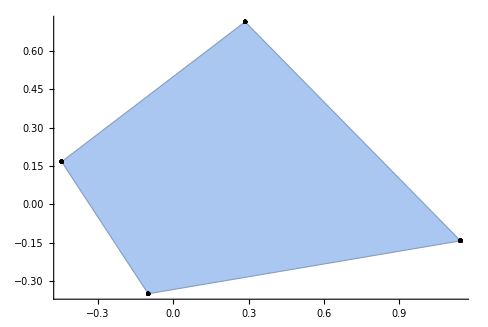

* * * * * * * * * * * * * * * *

* * *   NCPolyGroebner    * * *

* * * * * * * * * * * * * * * *

* Monomial order: x1≪ x2≪ (59254/62031+(36464 x1)/62031+(25069 x2)/124062)^-1

* Reduce and normalize initial set

> Initial set could not be reduced

* Computing initial set of obstructions

> MAJOR Iteration 1, 7 polys in the basis, 11 obstructions

> MAJOR Iteration 2, 9 polys in the basis, 14 obstructions

* Found Groebner basis with 9 polynomials

* * * * * * * * * * * * * * * *

-416/2261-(1549 x1)/2261-(328 x2)/2261+(13 x1**x1)/38+(302 x1**x2)/323+(302 x2**x1)/323+(429 x1**x1**x1)/646+x1**x2**x1

-2777/3553-(16521 x1)/7106-(2777 x2)/3553+(10207 x1**x1)/7106+(15863 x1**x2)/7106+(9664 x2**x1)/3553+(302 x2**x2)/323+(624 x1**x1**x1)/323+(429 x1**x1**x2)/646+(32 x1**x2**x1)/11+x1**x2**x2

-2777/3553-(16521 x1)/7106-(2777 x2)/3553+(10207 x1**x1)/7106+(9664 x1**x2)/3553+(15863 x2**x1)/7106+(302 x2**x2)/323+(624 x1**x1**x1)/323+(32 x1**x2**x1)/11+(429 x2**x1**x1)/646+x2**x2**x1

298/2261+(12 x1)/2261-(649 x2)/4522+(15 x1**x2)/34+(15 x2**x1)/34-(851 x2**x2)/646+(429 x2**x1**x2)/646+x2**x2**x2

```mathematica
(* Input free spectrahedra defining tuple to NCSE *)
quad1=DiagonalMatrix[{3,-1/2,-1,3/2}];
quad2=DiagonalMatrix[{2,3,-1,-2}];
quad={quad1,quad2};
ViewLMIGraphic[-quad]
(* Visualization of level 1 of the free quadrilateral *)
Level1ExtremePlot[-quad,PointCount-> 100]
(* Computation of NC Polynomials *)
SNC[x1,x2]
polys=QuadriArvesonPolynomials[quad,{x1,x2}];
polys[[1]]
polys[[2]]
polys[[3]]
polys[[4]]
```

We next check that these NC polynomials evaluate to zero on a few members of the Arveson boundary at level 2 of the free quadrilateral defined by quad. Note: Using Proposition 4.3, it is sufficient to only check level 2. We print the norm of the evaluation of our polynomials on these points.
Note: The FindExtremePoint function maximizes a linear functional over the specified level of the given free spectrahedron. Here we fix a weight vector to guarantee that the resulting tuple is an Arveson extreme point of the free quadrilateral.

```mathematica
(* Generate points *)
pt1=FindExtremePoint[-quad,2,WeightVector-> {-6729/4000,-112597/100000,171687/100000,47621/50000,-30391/50000,-28257/25000},DiagnosticLevel->0];
pt2=FindExtremePoint[-quad,2,WeightVector-> {18403/100000,-10949/20000,-12181/100000,-37719/50000,-4659/5000,175211/100000},DiagnosticLevel-> 0];
(* Check points are Arveson extreme in our free quadrilateral *)
ArvesonTest[-quad,pt1][[1]]
ArvesonTest[-quad,pt2][[1]]
(* Compute norms of evaluation of our NC polynomials on these points *)
Table[Norm[Eval[polys[[i]],{x1,x2},pt1]],{i,4}]
Table[Norm[Eval[polys[[i]],{x1,x2},pt2]],{i,4}]
```

True

True

{3.20358×10^-9,1.22755×10^-8,1.22755×10^-8,1.17471×10^-9}

{1.36202×10^-9,4.17349×10^-9,4.17349×10^-9,2.03488×10^-10}

Additionally we see that these polynomials do not evaluate to zero on a tuple which is a Euclidean (classical) extreme point of the free quadrilateral at level 2, but not an Arveson extreme point of the free quadrilateral.
Note: Similar to before, we fix a weight vector to guarantee that the resulting tuple is a Euclidean extreme point, but not an Arveson extreme point of the free quadrilateral.

```mathematica
(* Generate point *)
pt3=FindExtremePoint[-quad,2,WeightVector-> {-23939/50000,-148139/100000,1329/6250,18041/100000,7309/100000,-9121/6250},DiagnosticLevel-> 0];
(* Check point is Euclidean but not Arveson extreme *)
ArvesonTest[-quad,pt3][[1]]
EuclideanTest[-quad,pt3][[1]]
(* Compute norms of evaluation of our NC polynomials on the points *)
Table[Norm[Eval[polys[[i]],{x1,x2},pt3]],{i,4}]
```

False

True

{0.14748,0.502482,0.502482,0.0476348}

We now compute the projective map which sends the free square to the free quadrilateral defined by quad. In addition we show that this map sends Arveson extreme points of the free square to Arveson extreme points of the quad. 

Note: For the free square a tuple is Arveson extreme if and only if it is Euclidean extreme, so in this case there is no need to fix weight vectors.

```mathematica
(* Compute the projective map sending the free square to the free quadrilateral defined by quad *)
ProjMap=QuadrilateralProjectiveMap[NCSquare,quad];
ProjMap//MatrixForm
```

(59254/62031 | -26/93 | 52/667
21632/434217 | 260/651 | -156/667
28964/434217 | 104/651 | 208/667)

```mathematica
(* Generate random extreme points at level 2 of the free square and verify that they are Arveson extreme *)
sqpt1=FindExtremePoint[-NCSquare,2,DiagnosticLevel->0];
sqpt2=FindExtremePoint[-NCSquare,2,DiagnosticLevel-> 0];
ArvesonTest[-NCSquare,sqpt1][[1]]
ArvesonTest[-NCSquare,sqpt2][[1]]
```

True

True

```mathematica
(* Map the points to the free quadrilateral and verify that they are members of quad *)
qupt1=NCProjectiveMap[sqpt1,ProjMap];
qupt2=NCProjectiveMap[sqpt2,ProjMap];
view[qupt1]
view[qupt2]
Min[Eigenvalues[LMI[-quad,qupt1]]]
Min[Eigenvalues[LMI[-quad,qupt2]]]
```

{(-0.435935 | 0.0534657
0.0534657 | -0.108509),(0.153903 | -0.0801985
-0.0801985 | -0.337236)}

{(0.989399 | 0.408873
0.408873 | 0.0534582),(-0.168434 | 0.0681455
0.0681455 | -0.324424)}

-3.58369×10^-9

-5.61602×10^-10

```mathematica
(* Check the points are Arveson extreme in the free quadrilateral both using ArvesonTest and by verifying that they are annihilated by the NC polynomials which anihilate the Arveson boundary of quad. *)
ArvesonTest[-quad,qupt1][[1]]
ArvesonTest[-quad,qupt2][[1]]
Table[Norm[Eval[polys[[i]],{x1,x2},qupt1]],{i,4}]
Table[Norm[Eval[polys[[i]],{x1,x2},qupt2]],{i,4}]
```

True

True

{1.44397×10^-9,4.70037×10^-9,4.70037×10^-9,1.34061×10^-9}

{1.06317×10^-9,3.66661×10^-9,3.66661×10^-9,2.39327×10^-9}

## Example of non-Euclidean extreme point mapped to Euclidean extreme point.

We now give an of a tuple which is not Euclidean extreme that is mapped to a Euclidean extreme point under a invertible projective map.

```mathematica
(* Define the projective map and its inverse transpose, and the tuple X *)
```

```mathematica
V=1/280*{{306,0,54},{-54,63,-108},{27,127,27}};
W=Transpose[Inverse[V]];
X={1/Sqrt[2]*{{1,1},{1,-1}},{{1,0},{0,0}}};
```

```mathematica
(* Check that X is an element of the free square which is not Euclidean extreme. The Euclidean extreme check is performed in two ways. First we use the "EuclideanTest" command which checks the appropriate kernel condition for a tuple to be Euclidean extreme. Second we show that there are elements Y1 and Y2 of the free square of which X is a nontrivial convex combination *)

PositiveSemidefiniteMatrixQ[LMI[-NCSquare,X]]
EuclideanTest[-NCSquare,X]
Y1={1/Sqrt[2]*{{1,1},{1,-1}},{{1,0},{0,1}}};
Y2={1/Sqrt[2]*{{1,1},{1,-1}},{{1,0},{0,-1}}};
PositiveSemidefiniteMatrixQ[LMI[-NCSquare,Y1]]
PositiveSemidefiniteMatrixQ[LMI[-NCSquare,Y2]]
X==(Y1+Y2)/2
```

True

{False,{0,0.}}

True

True

True

```mathematica
(* We now map under the projective map defined by V and show that it is a Euclidean extreme point of the image of the free square under this map. Recall that the defining tuple for this image is equal to the image of the defining tuple of the free square under the projective map defined by W = Transpose[Inverse[V]]. We also check that the resulting free spectrahedron is bounded. *)
```

```mathematica
A=NCProjectiveMap[NCSquare,W];
PX=NCProjectiveMap[X,V];
BoundedQ[-A]
PositiveSemidefiniteMatrixQ[LMI[-A,PX]]
EuclideanTest[-A,PX]
```

True

True

{True,{0,0.0300585}}